102-41 x-57 x^2+26 x^3

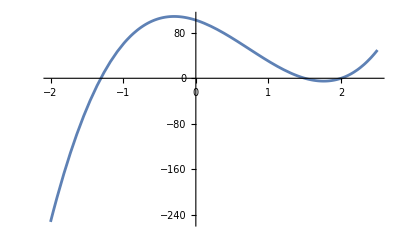
```mathematica
{{-Graphics-}, {□}, {□}}
```

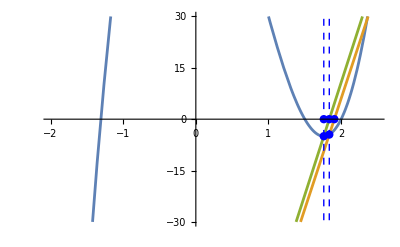

решение: 1.99994 Найдено на шаге: 2

```mathematica
{{(*на данном графике видно что уравнение имеет три действительных корня на отрезке [-2,3]. Эти корни расположены в интервалах (-2,-1), (1,2)*)}, {□}}
```

```mathematica
f[x_]=x^6-3*x^5-9*x^4+19*x^3+12*x^2-36*x+16;
```

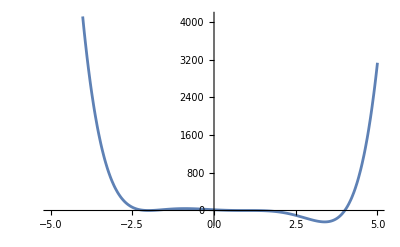

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
Solve[f[x]==0]
```

{{x→-2},{x→-2},{x→1},{x→1},{x→1},{x→4}}

```mathematica
NSolve[f[x]==0]
```

{{x→-2.},{x→-2.},{x→1.},{x→1.},{x→1.},{x→4.}}

```mathematica
Roots[f[x]==0,x]
```

x==-2||x==-2||x==1||x==1||x==1||x==4

```mathematica
Factor[f[x]]
```

(-4+x) (-1+x)^3 (2+x)^2

```mathematica
(*видно что данное уравнение f(х) имеет три корня, причем корень х=1 является трехкратным, а корень х=-2 двукратным *)
```

```mathematica
FindRoot[f[x]==0,{x,-3}](*здесь находим корень с помощью начального приближения, в данном случае нач. приближение равно -3*)
```

{x→-2.}

```mathematica
FindRoot[f[x],{x,2}](*в данном случае нач. приближение равно 2*)
```

{x→1.}

```mathematica
f[x_]=x*Log3[x]+x^2-5*x+2;
ep=10^(-3);
Plot[f[x],{x,-10,10}]
```

-Graphics-